```mathematica
Manipulate[Graphics[{
Disk[{2,2},10];
(*disegno acqua*)
LightBlue,
If[i≠0,
{
Rectangle[{-1,0},{1,i}],
Scale[Disk[{0,i},1],{1,.5}],
Scale[Disk[{0,0},1],{1,.5}],
Cyan,
Scale[Circle[{0,i},1],{1,.5}]
}
],
(*disegno bottiglia*)
Black,
Scale[Circle[{0,6},.3],{1,.5}],
Scale[Circle[{0,4.6},.3],{1,.5}],
Line[{{-.3,4.6},{-.3,6}}],
Line[{{.3,4.6},{.3,6}}],
Scale[Circle[{0,4},1],{1,.5}], (*cerchio superiore*)
Line[{{-1,0},{-1,4}}],(*linea sinistra*)
Line[{{1,0},{1,4}}],(*linea destra*)
Scale[Circle[{0,0},1],{1,.5}](*cerchio base*)
},PlotRange->7]
(*paramentri primo slider*)
,{{
i,(*variabile agganciata allo slider*)
0,(*valore iniziale*)
"numerator"(*etichetta dello slider*)
},
0,4,(*range*)
1,(*step di modifica*)
Appearance->"Labeled"}
]
```

```mathematica
Graphics[
{
Scale[Circle[{0,4},.9],{1,.5}],
Line[{{-.9,4},{-1,2.5}}],
Line[{{.9,4},{1,2.5}}],
Scale[Circle[{0,2.1},1],{1,.75}],
LightBlue,
Scale[Disk[{0,2.5},1],{1,.5}],
Rectangle[{0-1,2.1},{1,2.5}],
Scale[Disk[{0,2.1},1],{1,.75}],
Black,
Scale[Circle[{0,2.5},1],{1,.5}],
Scale[Circle[{0,0},1],{1,.5}],
White,
EdgeForm[Black],
Rectangle[{-.15,0},{.15,1.35}]
},PlotRange->6
]
```

-Graphics-

```mathematica
Manipulate[
Pane[
With[{b=b},
DisplayForm@Text[Style[
Grid[{
{
Graphics[
{
FaceForm[],
Table[
{EdgeForm[Black],
Disk[{0,0},1,{0,i}]
},
{i,0,2 Pi,2Pi/b}
]
},ImageSize->{200,200},
PlotRange->1,PlotRangePadding->.05
],SpanFromLeft,SpanFromLeft,SpanFromLeft
}},Frame->None,ItemSize->{{1.2,.5,1.2,.5,2.75,.5,1.75},Automatic}],40]]],ImageSize->{500,600},ImageMargins->20],{{b,10,"denominator"},1,10,1,Appearance->"Labeled"}]
```

```mathematica
peon[x_]:=Piecewise[{
{1-x/2,0<x<1},
{1/2,1<x<3},
{3/4-(x-7/2)^2,3<x<4}
}];
RevolutionPlot3D[{peon[y],y},{y,0,4},PlotRange->All]
```

-Graphics3D-

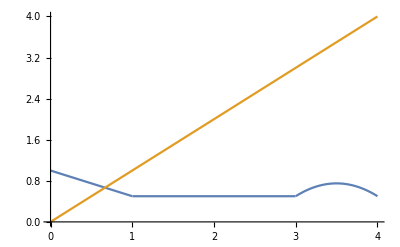

```mathematica
peon[x_]:=Piecewise[{
{1-x/2,0<x<1},
{1/2,1<x<3},
{3/4-(x-7/2)^2,3<x<4}
}];
Plot[{peon[y],y},{y,0,4},PlotRange->All]
```

```mathematica
getTipoFrazione[numeratore_,denominatore_] := (
		tipo = "frazione ";
		If[numeratore==denominatore || Mod[numeratore,denominatore]==0,tipo =tipo <>"apparente",
			If[numeratore<denominatore,tipo =tipo <>"propria",
				If[numeratore>denominatore,tipo =tipo <>"impropria"];
			]
		];
		tipo
	)
```

```mathematica
getEsempioTipoFrazione[] := (
	
		Manipulate[
			coloreNumeratore = Blue; (*colore per il numeratore*)
			coloreDenominatore = Red;(*colore per il denominatore*)
			Graphics[{
		Disk[{2,2},10];
		(*disegno acqua*)
		LightBlue,
		If[i≠0,
		{
		Rectangle[{-1,0},{1,i}],
		Scale[Disk[{0,i},1],{1,.5}],
		Scale[Disk[{0,0},1],{1,.5}],
		Cyan,
		Scale[Circle[{0,i},1],{1,.5}]
		}
		],
		(*disegno bottiglia*)
		Black,
		Scale[Circle[{0,6},.3],{1,.5}],
		Scale[Circle[{0,4.6},.3],{1,.5}],
		Line[{{-.3,4.6},{-.3,6}}],
		Line[{{.3,4.6},{.3,6}}],
		Scale[Circle[{0,4},1],{1,.5}], (*cerchio superiore*)
		Line[{{-1,0},{-1,4}}],(*linea sinistra*)
		Line[{{1,0},{1,4}}],(*linea destra*)
		Scale[Circle[{0,0},1],{1,.5}](*cerchio base*)
		},PlotRange->7],
			{{numeroBottiglie,
				1,(*valore iniziale slider numeratore*)
				Style["Numero bottiglie",Directive[coloreNumeratore,Large]]
				},
				1,5,1,(*valore iniziale, valore finale, step di incremento/decremento slider*)
				Appearance->{"Labeled"},
				AppearanceElements->{"InputField"},
				LabelStyle->Directive[coloreNumeratore,Large],
				ImageSize->400
			},(*--fine slider numeratore*)
			{{numeroBicchieri,2,Style["Numero bicchieri",Directive[coloreDenominatore,Large]]},1,5,1,
				Appearance->{"Labeled"},
				AppearanceElements->{"InputField"},(*rimuovo tutto tranne l'inputField*)
				LabelStyle->Directive[coloreDenominatore,Large],ImageSize->400}
			]
	)
```

```mathematica
getEsempioTipoFrazione[]
```

```mathematica
Manipulate[
objBottiglie = {};
plotRange = 15;
offsetX = -7;
offsetY = 3;
For[i = 0, i< numeroBottiglie,i++,
AppendTo[objBottiglie,{Black,Circle[{(i*3.5)+offsetX,0 + offsetY},1]}]
];
objBicchieri = {};
offsetX = -9;
offsetY = -6;
For[i = 0, i< numeroBicchieri,i++,
AppendTo[objBicchieri,{Black,Circle[{(i*2)+offsetX,0 + offsetY},1]}]
];
Graphics[{
objBottiglie,
objBicchieri
},PlotRange->{{-10,10},{-8,8}}]
(*paramentri primo slider*)
,{
{numeroBottiglie,1,(*valore iniziale slider numeratore*)
		Style["Numero bottiglie",Directive[coloreNumeratore,Large]]},
	1,5,1,(*valore iniziale, valore finale, step di incremento/decremento slider*)
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},
	LabelStyle->Directive[coloreNumeratore,Large],
	ImageSize->170
	},(*--fine slider numeratore*)
{
{numeroBicchieri,2,Style["Numero bicchieri",Directive[coloreDenominatore,Large]]}
,1,10,1,
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},(*rimuovo tutto tranne l'inputField*)
	LabelStyle->Directive[coloreDenominatore,Large],ImageSize->170}
]
```